```mathematica
(* Find all the zero positions *)
f[x_] := r*x + 4*x^3 -9*x^5
xstar = Solve[r*x + 4*x^3 -9*x^5 ==0,x] // Simplify
```

{{x→0},{x→-1/3 √(2-√(4+9 r))},{x→1/3 √(2-√(4+9 r))},{x→-1/3 √(2+√(4+9 r))},{x→1/3 √(2+√(4+9 r))}}

```mathematica
xstar1[r_] = 0 ;
xstar2[r_] = -1/3 √(2-√(4+9 r));
xstar3[r_] = 1/3 √(2-√(4+9 r));
xstar4[r_] =-1/3 √(2+√(4+9 r));
xstar5[r_] = 1/3 √(2+√(4+9 r));
xstar1[r_] = 0;
```

```mathematica
(* Determine which xstars are stable and which are instable *)
dir1[r_]= D[f[x],x]/.xstar[[1]]
dir2[r_]= D[f[x],x]/.xstar[[2]]
dir3[r_]= D[f[x],x]/.xstar[[3]]
dir4[r_]= D[f[x],x]/.xstar[[4]]
dir5[r_]= D[f[x],x]/.xstar[[5]]

(* eval at r = -0.2*)
r1 = -0.2
dir1[r1]
dir2[r1]
dir3[r1]
dir4[r1]
dir5[r1]
```

r

r+4/3 (2-√(4+9 r))-5/9 (2-√(4+9 r))^2

r+4/3 (2-√(4+9 r))-5/9 (2-√(4+9 r))^2

r+4/3 (2+√(4+9 r))-5/9 (2+√(4+9 r))^2

r+4/3 (2+√(4+9 r))-5/9 (2+√(4+9 r))^2

-0.2

-0.2

0.340658

0.340658

-2.29621

-2.29621

```mathematica
0.3406575088170066
```

0.340658 ^3

```mathematica
0.3406575088170066 ^3
```

0.340658 ^3

```mathematica
Manipulate[Plot[r*x + 4*x^3 -9*x^5,{x,-1,1}], {r,-2,2}]
```

```mathematica
(* Determine a range for r*)
rmin = -1;
rmax = 1;
```

```mathematica
(* First solution is for r < 0*)
plot1 = Plot[xstar1[r], {r,rmin,0}, PlotStyle->{Red}];
plot11 = Plot[xstar1[r], {r,0,rmax}, PlotStyle->{Red, Dashed}];
plot2 = Plot[xstar2[r], {r,rmin,rmax}, PlotStyle->{Red, Dashed}];
plot3 = Plot[xstar3[r], {r,rmin,rmax}, PlotStyle->{Red, Dashed}];
plot4 = Plot[xstar4[r], {r,rmin,rmax}, PlotStyle->{Red}];
plot5 = Plot[xstar5[r], {r,rmin,rmax}, PlotStyle->{Red}];
```

```mathematica
(* Combine all plots together *)
Show[plot1, plot11, plot2, plot3, plot4, plot5,AxesLabel->{r,x}, PlotRange->{{rmin,rmax},{rmin,rmax}}]
```

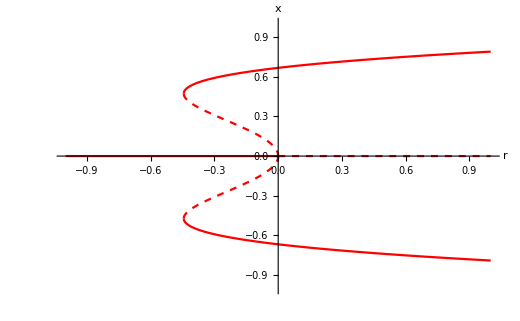
```mathematica
-Graphics-
-Graphics-
```

At the point - 4/9 saddle - node bifurcation occurs . If approaching from the left, so r < -4/9, one jumps from 1 to 3 FPs if r = -4/9. In the moment when r > -4/9 another two FPs are created, so a total of five exists . Three of them are stable, as can be seen in the plot with the continuous lines, and two are unstable (dashed lines) . Ar the origin 2 FPs are lost, and the stable FP on the x = 0 line become s unstable. There an subcritical pitchform bifurcation occurs.

```mathematica
(* Find the saddle-node bifurcations analytically *)
df[x_,r_] = r + 12 x^2 - 45 x^4;
```

```mathematica
b1[r_] = df[x,r] /. xstar[[3]]
```

r+4/3 (2-√(4+9 r))-5/9 (2-√(4+9 r))^2

```mathematica
(* question b -> where is r_c*)
Solve[b1[r]==0, r]
```

```mathematica
{{r->-4/9},{r->0}}
```